# trajectory of elecron

```mathematica
<<Graphics`Graphics3D`
```

## 100 orbit

```mathematica
fz=Compile[{{x,_Real,1},{dt,_Real}},Module[{},Return[x-x/Sqrt[x.x]*dt+Sqrt[dt]*Table[Sum[Random[Real,{0,1}],{12}]-6,{Length[x]}]]]]
```

CompiledFunction[…]

```mathematica
dt:=0.05
```

```mathematica
n:=5002
```

```mathematica
x=Table[{0.0,0.0,0.0},{n}];
```

```mathematica
x[[1]]={1.0,1.0,1.0};
```

```mathematica
Timing[Do[x[[i]]=fz[x[[i-1]],dt],{i,2,n}]][[1]]
```

0.123721

```mathematica
ListPointPlot3D[x,AxesLabel->{"X","Y","Z"},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Options[ListPointPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionBoundaryStyle→Automatic,RegionFunction→(True&),RotationAction→Fit,ScalingFunctions→None,SphericalRegion→Automatic,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1}}

## 211 orbit

Modified for Mathematica 5 on 9 September 2003

```mathematica
fz=Compile[{{y,_Real,2},{dt,_Real}},Module[{x},
x=y;
Do[x[[i+1]]=x[[i]]+({1/x[[i,1]],0.0,0.0}-0.5*x[[i]]/Sqrt[x[[i]].x[[i]]])*dt+Sqrt[dt]*Table[Sum[Random[Real,{0,1}],{12}]-6,{3}]
,{i,Length[x]-1}];Return[x]
]]
```

CompiledFunction[…]

```mathematica
dt:=0.01
```

```mathematica
n:=100000
```

```mathematica
dn:=n/2500
```

```mathematica
x=Table[{0.0,0.0,0.0},{n}];
```

```mathematica
y=Table[{0.0,0.0,0.0},{n}];
```

```mathematica
x[[1]]={-1.,0.,0.};
```

```mathematica
y[[1]]={1.,0.,0.};
```

```mathematica
Timing[x=fz[x,dt]][[1]]
```

127.205

```mathematica
Timing[y=fz[y,dt]][[1]]
```

127.431

```mathematica
x1=Table[x[[i]],{i,1,Length[x],dn}];
```

```mathematica
y1=Table[y[[i]],{i,1,Length[y],dn}];
```

```mathematica
z=Join[x1,y1];
```

```mathematica
ListPointPlot3D[z,AxesLabel->{"x","y","z"},ViewPoint->{1.300, -2.400, 2.000}]
```

-Graphics3D-

```mathematica
g1=Graphics3D[{Hue[0.05],Line[x1]}]
```

-Graphics3D-

```mathematica
g2=Graphics3D[{Hue[0.75],Line[y1]}]
```

-Graphics3D-

```mathematica
Show[{g1,g2},Axes->True,AxesLabel->{"X","Y","Z"}];
```

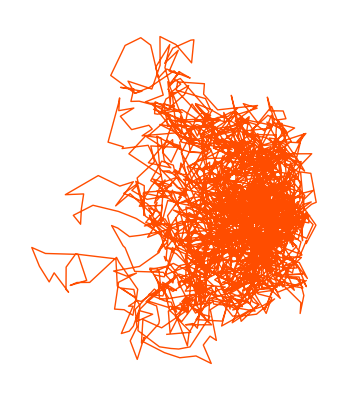

```mathematica
g3=Graphics[{Hue[0.05],Line[Table[{x1[[i,1]],x1[[i,2]]},{i,Length[x1]}]]}]
```

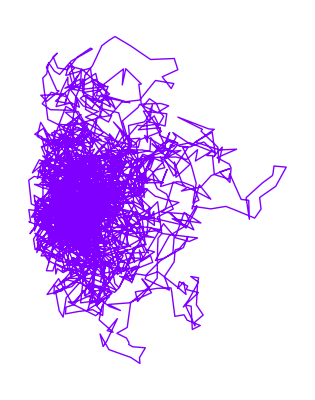

```mathematica
g4=Graphics[{Hue[0.75],Line[Table[{y1[[i,1]],y1[[i,2]]},{i,Length[y1]}]]}]
```

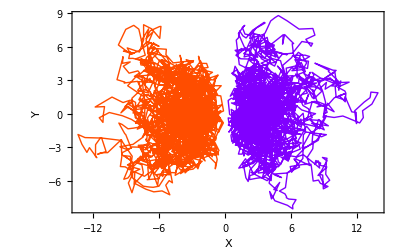

```mathematica
Show[g3,g4,Frame->True,Axes->False,FrameLabel->{"X","Y"}]
```

```mathematica
Show[g1,g2,Frame->True,Axes->False,FrameLabel->{"X","Y"}]
```

-Graphics3D-

References
Excel de Manabu Ryoushi Rikigaku (Learning about Quantum Mechanics with Excel), 
Kunio Yasue,  Blue Backs,  Kodansha,  2001
(in japanese)